```mathematica
imp=Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\pock_saege_winkel1.tab","Table"];
data=Drop[imp,1];
data1=Transpose[Delete[Transpose[data],3]];
data2=Transpose[Delete[Transpose[data],2]];
```

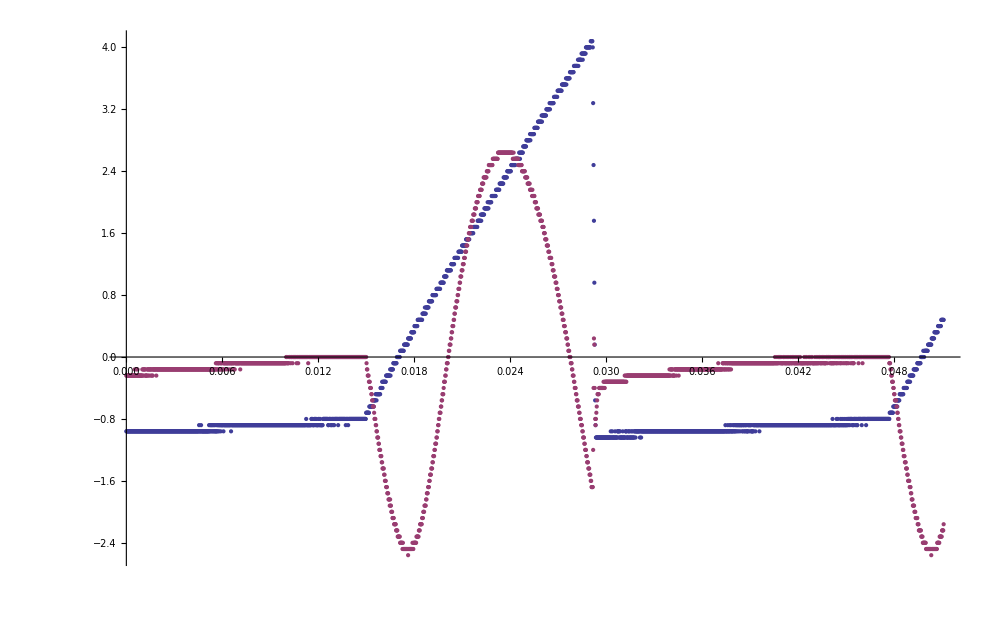

```mathematica
ListPlot[{data1,data2},ImageSize->1000]
```